```mathematica
SetDirectory["/Users/bittner/Dropbox/QuTip/Spin-Chain-OTOC"]
figdir = "/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures";
```

/Users/bittner/Library/CloudStorage/Dropbox/QuTip/Spin-Chain-OTOC

```mathematica
s1 = Import["Noise_Synchro1z_gamma=0.05.csv"];
s2 = Import["Noise_Synchro2z_gamma=0.05.csv"];
order = Import["Noise_Synchro_order_param_gamma=0.05.csv"]//Flatten;
Δϕ= Import["Noise_Synchro_Phase_diff_gamma=0.05.csv"]//Flatten;
plv = Import["Noise_Synchro_PLV_gamma=0.05.csv"]//Flatten;
```

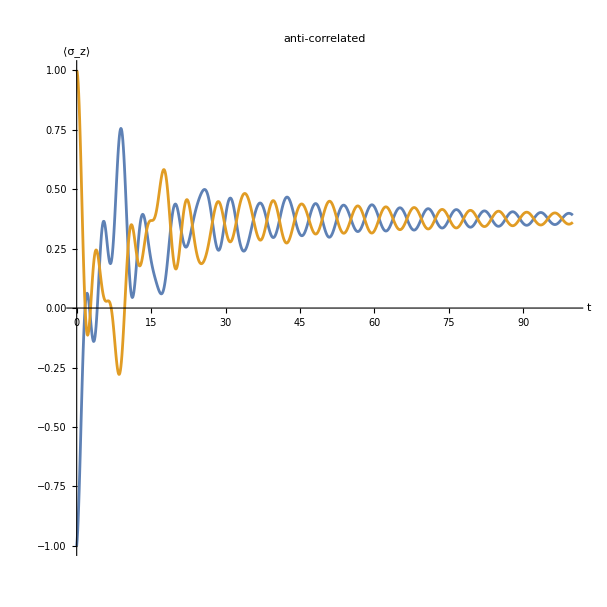

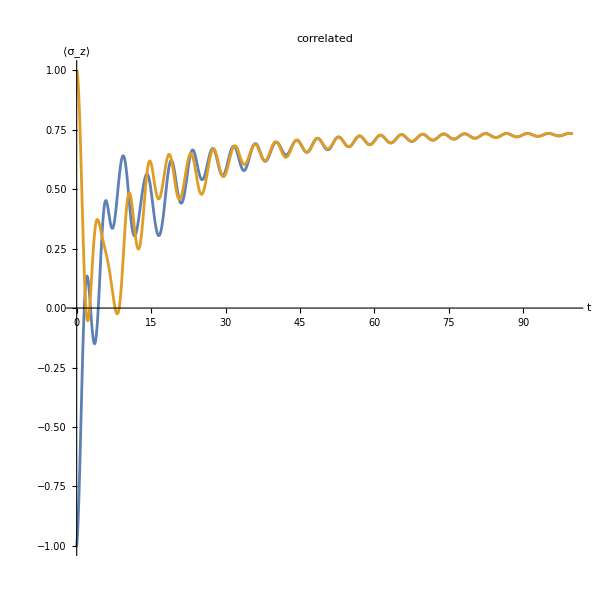

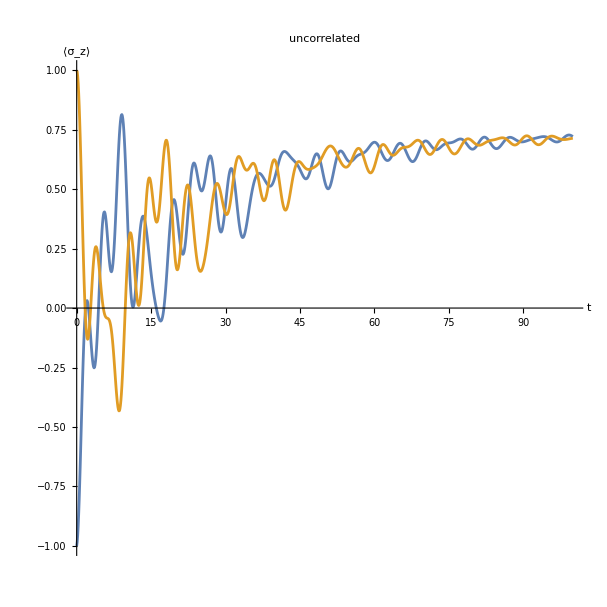

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/SigmaZ_anticorrelated.pdf

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/SigmaZ_correlated.pdf

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/SigmaZ_uncorrelated.pdf

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/OrderParam.pdf

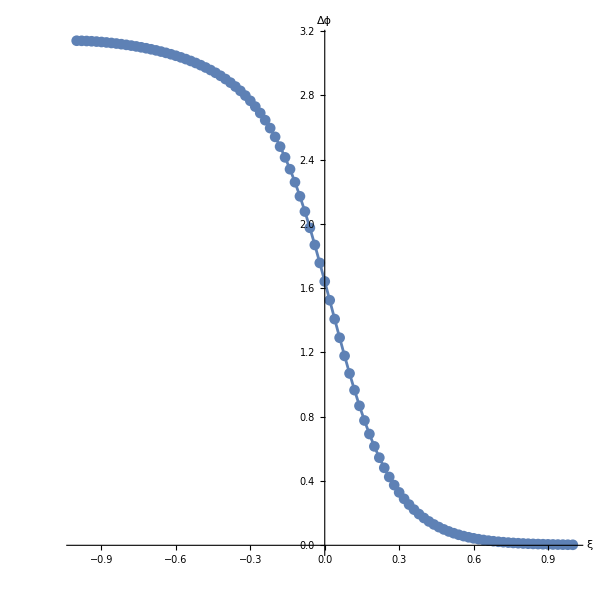

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/OrderParam.pdf

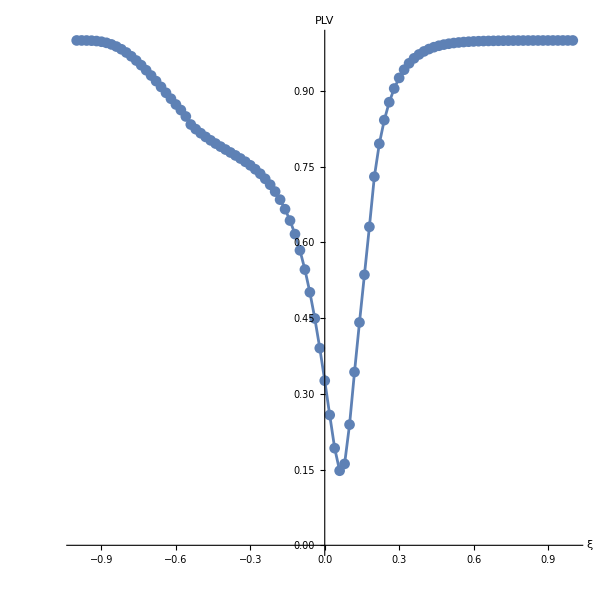

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Phase_Locking_Value.pdf

```mathematica
plot1 =ListPlot[{s1[[1]],s2[[1]]},
Joined->True,
PlotRange->All,
DataRange->{0,100},
AspectRatio->1,
AxesLabel->{"t","⟨σ_z⟩"},
LabelStyle->16,
PlotLabel->"anti-correlated"]
plot2 = ListPlot[{s1[[-1]],s2[[-1]]},
Joined->True,
PlotRange->All,
DataRange->{0,100},
AspectRatio->1,
AxesLabel->{"t","⟨σ_z⟩"},
LabelStyle->16,
PlotLabel->"correlated"]

plot3 = ListPlot[{s1[[50]],s2[[50]]},
Joined->True,
PlotRange->All,
DataRange->{0,100},
AspectRatio->1,
AxesLabel->{"t","⟨σ_z⟩"},
LabelStyle->16,
PlotLabel->"uncorrelated"]

Export[figdir<>"/SigmaZ_anticorrelated.pdf",plot1]
Export[figdir<>"/SigmaZ_correlated.pdf",plot2]
Export[figdir<>"/SigmaZ_uncorrelated.pdf",plot3]
Export[figdir<>"/OrderParam.pdf",plot3]





ListPlot[order,Joined->True,
AxesLabel->{"ξ","Δϕ"},
PlotRange->{0,Pi},
PlotMarkers->Automatic,
AspectRatio->1,
LabelStyle->24,
DataRange->{-1,1}
]

Export[figdir<>"/OrderParam.pdf",%]

ListPlot[plv,Joined->True,
AxesLabel->{"ξ","PLV"},
PlotRange->{0,1},
PlotMarkers->Automatic,
AspectRatio->1,
LabelStyle->24,
DataRange->{-1,1}
]

Export[figdir<>"/Phase_Locking_Value.pdf",%]
```

```mathematica
s1x = Import["Noise_Synchro1x_gamma=0.05.csv"];
s1y = Import["Noise_Synchro1y_gamma=0.05.csv"];
s1z = Import["Noise_Synchro1z_gamma=0.05.csv"];
s2x = Import["Noise_Synchro2x_gamma=0.05.csv"];
s2y = Import["Noise_Synchro2y_gamma=0.05.csv"];
s2z = Import["Noise_Synchro2z_gamma=0.05.csv"];
```

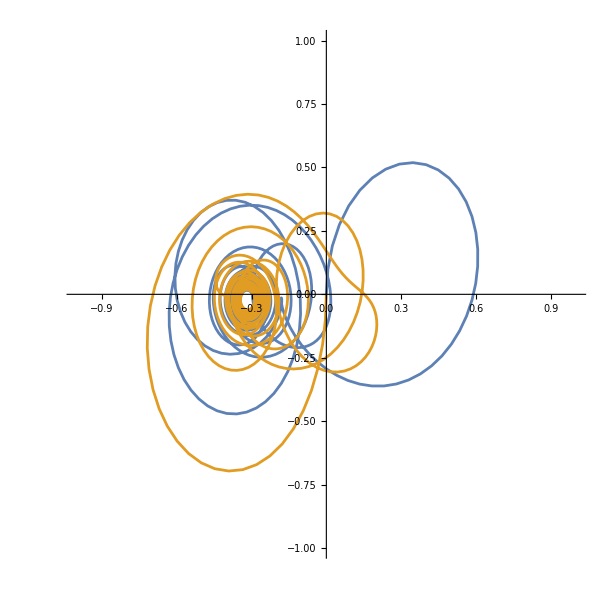

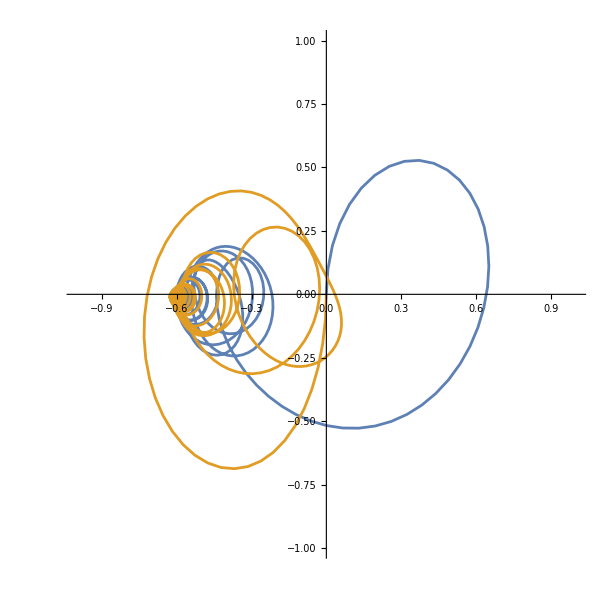

```mathematica
ListPlot[{{s1x[[1]],s1y[[1]]}//Transpose,
{s2x[[1]],s2y[[1]]}//Transpose},Joined->True,PlotRange->{{-1,1},{-1,1}},
AspectRatio->1]

ListPlot[{{s1x[[-1]],s1y[[-1]]}//Transpose,
{s2x[[-1]],s2y[[-1]]}//Transpose},Joined->True,PlotRange->{{-1,1},{-1,1}},
AspectRatio->1]
```

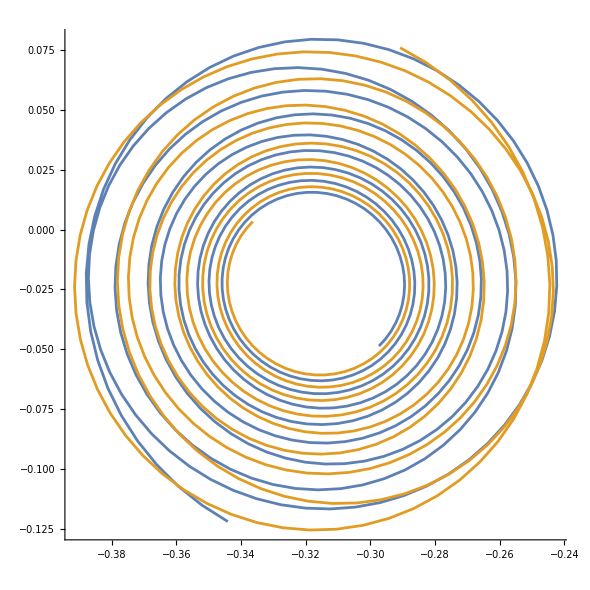

```mathematica
nn = 500;

ListPlot[
{
Take[{s1x[[1]],s1y[[1]]}//Transpose,-nn],
Take[{s2x[[1]],s2y[[1]]}//Transpose,-nn]},
Joined->True,
AspectRatio->1,
PlotRange->Automatic
]
```

### Analysis of the steady-states

```mathematica
base = "NoiseSynchro_Entropy_Scan_test2_";
entro10 = Import[base<>"1.0.csv"];
entro50 = Import[base<>"0.5.csv"];
entro375 = Import[base<>"0.375.csv"];
entro25 = Import[base<>"0.25.csv"];
entro1725 = Import[base<>"0.1725.csv"];
entro125 = Import[base<>"0.125.csv"];
entro1 = Import[base<>"0.1.csv"];
entro075 = Import[base<>"0.075.csv"];
entro05 = Import[base<>"0.05.csv"];
entro025 = Import[base<>"0.025.csv"];
entro01 = Import[base<>"0.01.csv"];
entro0075 = Import[base<>"0.0075.csv"];
entro005 = Import[base<>"0.005.csv"];
entro0025 = Import[base<>"0.0025.csv"];
entro00125 = Import[base<>"0.00125.csv"];
entro001 = Import[base<>"0.001.csv"];


base = "NoiseSynchro_Discord_Scan_test2_";
disco10 = Import[base<>"1.0.csv"];
disco50 = Import[base<>"0.5.csv"];
disco375 = Import[base<>"0.375.csv"];
disco25 = Import[base<>"0.25.csv"];
disco1725 = Import[base<>"0.1725.csv"];
disco125 = Import[base<>"0.125.csv"];
disco1 = Import[base<>"0.1.csv"];
disco075 = Import[base<>"0.075.csv"];
disco05 = Import[base<>"0.05.csv"];
disco025 = Import[base<>"0.025.csv"];
disco01 = Import[base<>"0.01.csv"];
disco0075 = Import[base<>"0.0075.csv"];
disco005 = Import[base<>"0.005.csv"];
disco0025 = Import[base<>"0.0025.csv"];
disco00125 = Import[base<>"0.00125.csv"];
disco001 = Import[base<>"0.001.csv"];

base = "NoiseSynchro_DiscordExact_Scan_test2_";
discoE10 = Import[base<>"1.0.csv"];
discoE50 = Import[base<>"0.5.csv"];
discoE375 = Import[base<>"0.375.csv"];
discoE25 = Import[base<>"0.25.csv"];
discoE1725 = Import[base<>"0.1725.csv"];
discoE125 = Import[base<>"0.125.csv"];
discoE1 = Import[base<>"0.1.csv"];
discoE075 = Import[base<>"0.075.csv"];
discoE05 = Import[base<>"0.05.csv"];
discoE025 = Import[base<>"0.025.csv"];
discoE01 = Import[base<>"0.01.csv"];
discoE0075 = Import[base<>"0.0075.csv"];
discoE005 = Import[base<>"0.005.csv"];
discoE0025 = Import[base<>"0.0025.csv"];
discoE00125 = Import[base<>"0.00125.csv"];
discoE001 = Import[base<>"0.001.csv"];
```

-Graphics-

-Graphics-

-Graphics-

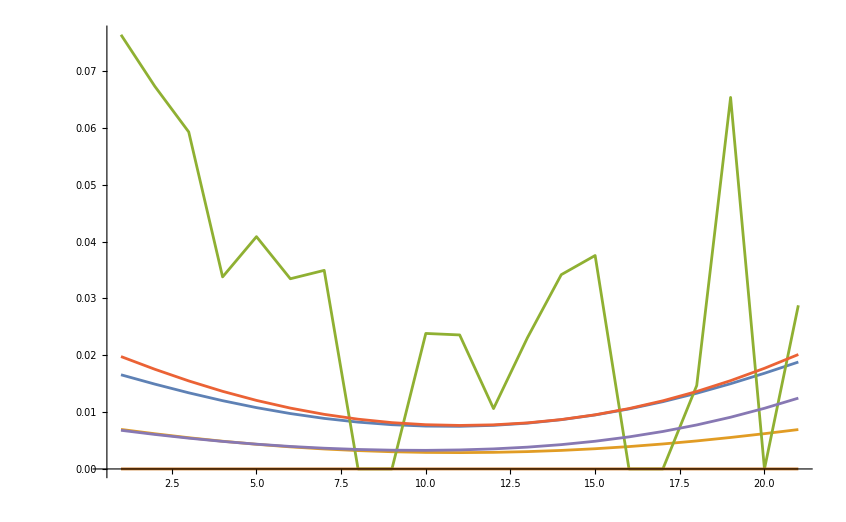

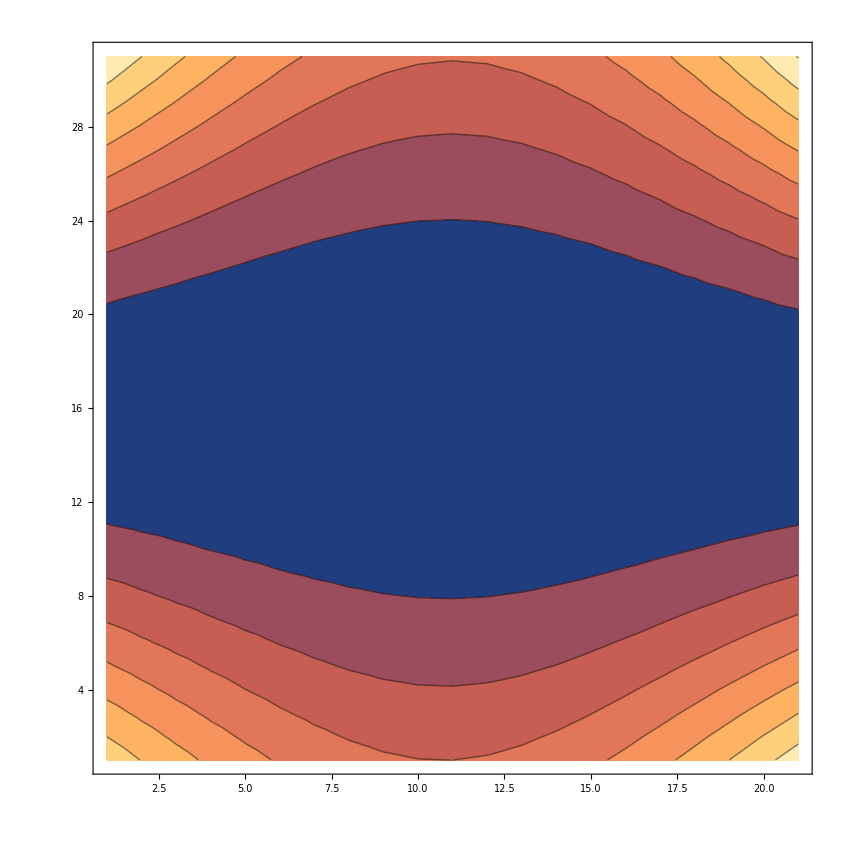

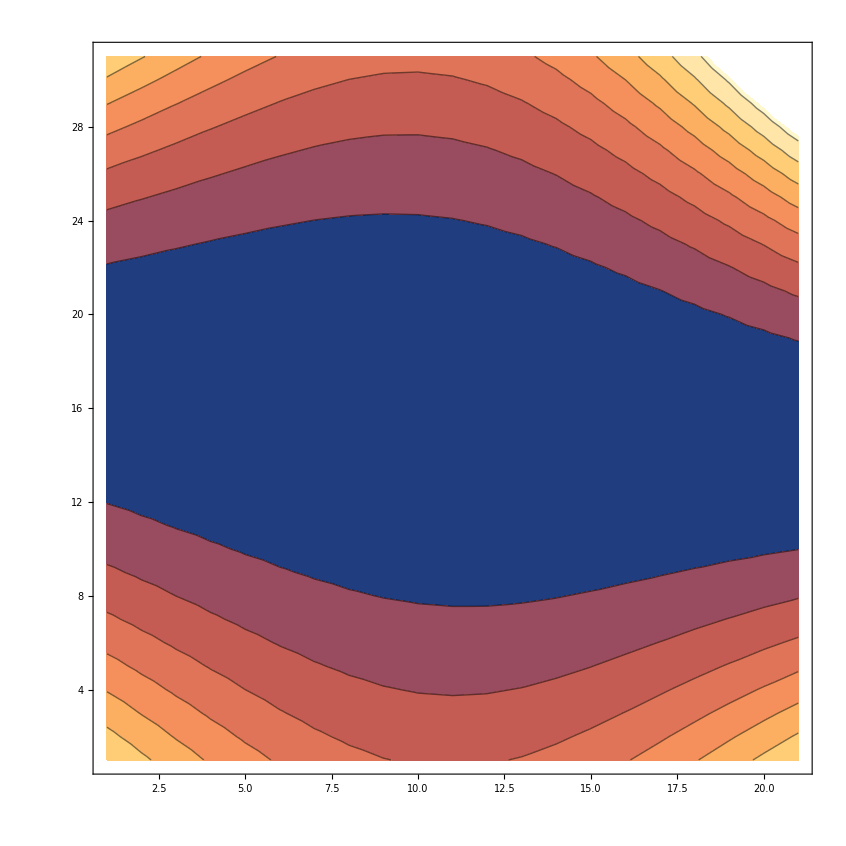

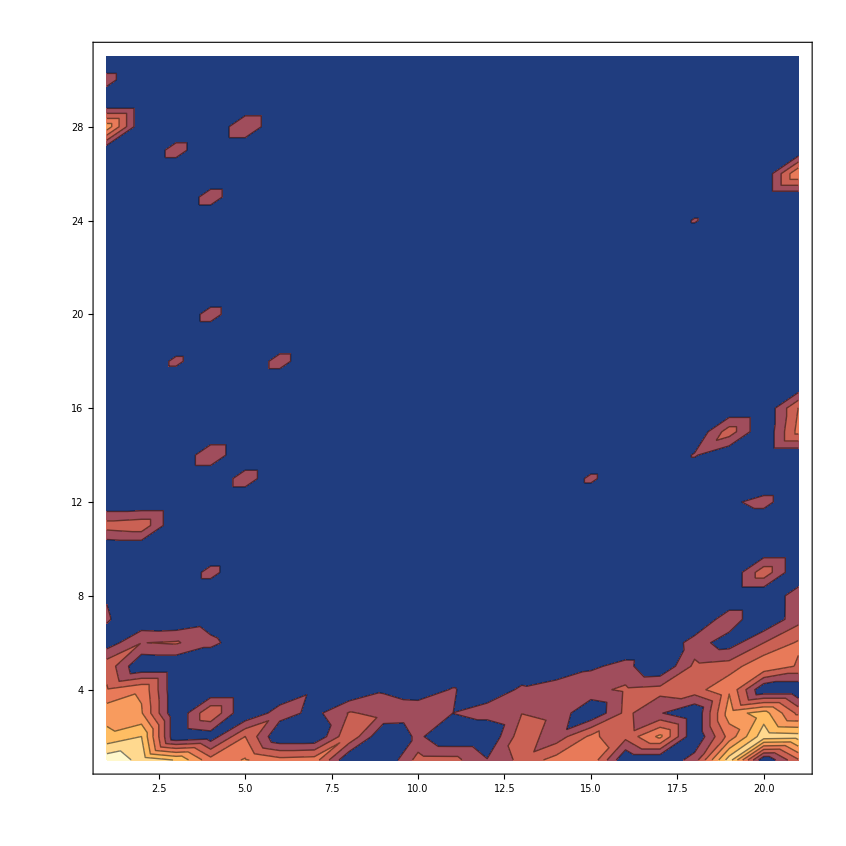

```mathematica
Table[jval,{jval,-1,1,N[2/30]}];
Dimensions[entro01];
ListPlot[entro01,Joined->True,PlotRange->All,PlotLabels->Table[jval,{jval,-1,1,N[2/30]}]]
ListPlot[disco01,Joined->True,PlotRange->All,PlotLabels->Table[jval,{jval,-1,1,N[2/30]}]]
ListPlot[discoE01,Joined->True,PlotRange->All,PlotLabels->Table[jval,{jval,-1,1,N[2/30]}]]


ListPlot[{entro01[[1]],disco01[[1]],discoE01[[1]],entro01[[-1]],disco01[[-1]],discoE01[[-1]]},Joined->True,PlotRange->All]


ListContourPlot[entro01]
ListContourPlot[disco01]
ListContourPlot[discoE01,PlotRange->All]
```

```mathematica
Dimensions[entro10]
```

{31,21}

```mathematica
gamval = {1.0,0.5,0.375,.25,0.1725,0.125,0.1,0.075,0.05,0.025,0.01,0.0075,0.005,0.0025,0.00125,0.001};
nn = 16
```

16

```mathematica
Dimensions[entro1]

Dimensions[Transpose[entro1][[11]]]
```

{31,21}

{31}

```mathematica
ξlen = Length[Transpose[entro001]];
Print[ξlen]
nn = Ceiling[ξlen/2]
ListPlot[
{Transpose[entro10][[nn]],
Transpose[entro50][[nn]],
Transpose[entro375][[nn]],
Transpose[entro25][[nn]],
Transpose[entro1725][[nn]],
Transpose[entro125][[nn]],
Transpose[entro1][[nn]],
Transpose[entro075][[nn]],
Transpose[entro05][[nn]],
Transpose[entro025][[nn]],
Transpose[entro01][[nn]],
Transpose[entro0075][[nn]],
Transpose[entro005][[nn]],
Transpose[entro0025][[nn]],
Transpose[entro00125][[nn]],
Transpose[entro001][[nn]]},
PlotMarkers->Automatic,
LabelStyle->16,
Joined->True,
AspectRatio->1,
PlotLabels->gamval,
PlotRange->Automatic,
DataRange->{-1,1},
AxesLabel->{"J_xy","I(σ_A|σ_B)"},
PlotLabel->"ξ=0"]

Export[figdir<>"/Mutual_Entropy_at_xi=0.pdf",%]

ξlen = Length[Transpose[entro001]];
Print[ξlen]
nn = Ceiling[ξlen/2]

nn  =1
ListPlot[
{Transpose[entro10][[nn]],
Transpose[entro50][[nn]],
Transpose[entro375][[nn]],
Transpose[entro25][[nn]],
Transpose[entro1725][[nn]],
Transpose[entro125][[nn]],
Transpose[entro1][[nn]],
Transpose[entro075][[nn]],
Transpose[entro05][[nn]],
Transpose[entro025][[nn]],
Transpose[entro01][[nn]],
Transpose[entro0075][[nn]],
Transpose[entro005][[nn]],
Transpose[entro0025][[nn]],
Transpose[entro00125][[nn]],
Transpose[entro001][[nn]]},
PlotMarkers->Automatic,
LabelStyle->16,
Joined->True,
AspectRatio->1,
PlotLabels->gamval,
PlotRange->Automatic,
DataRange->{-1,1},
AxesLabel->{"J_xy","I(σ_A|σ_B)"},
PlotLabel->"ξ=-1"]

Export[figdir<>"/Mutual_Entropy_at_xi=-1.pdf",%]


nn  =21
ListPlot[
{Transpose[entro10][[nn]],
Transpose[entro50][[nn]],
Transpose[entro375][[nn]],
Transpose[entro25][[nn]],
Transpose[entro1725][[nn]],
Transpose[entro125][[nn]],
Transpose[entro1][[nn]],
Transpose[entro075][[nn]],
Transpose[entro05][[nn]],
Transpose[entro025][[nn]],
Transpose[entro01][[nn]],
Transpose[entro0075][[nn]],
Transpose[entro005][[nn]],
Transpose[entro0025][[nn]],
Transpose[entro00125][[nn]],
Transpose[entro001][[nn]]},
PlotMarkers->Automatic,
LabelStyle->16,
Joined->True,
AspectRatio->1,
PlotLabels->gamval,
PlotRange->Automatic,
DataRange->{-1,1},
AxesLabel->{"J_xy","I(σ_A|σ_B)"},
PlotLabel->"ξ=+1"]

Export[figdir<>"/Mutual_Entropy_at_xi=+1.pdf",%]
```

21

11

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_Entropy_at_xi=0.pdf

21

11

1

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_Entropy_at_xi=-1.pdf

21

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_Entropy_at_xi=+1.pdf

```mathematica
nn = 1;
ListPlot[
{entro10[[nn]],
entro50[[nn]],
entro375[[nn]],
entro25[[nn]],
entro1725[[nn]],
entro125[[nn]],
entro1[[nn]],
entro075[[nn]],
entro05[[nn]],
entro025[[nn]],
entro01[[nn]],
entro0075[[nn]],
entro005[[nn]],
entro0025[[nn]],
entro00125[[nn]],
entro001[[nn]]},
PlotLabels->gamval,
PlotMarkers->None,
LabelStyle->16,
Joined->True,
AspectRatio->1,
DataRange->{-1,1},
AxesLabel->{None,Style["I(A:B)",20]},
Epilog->{ {Style[Text["ξ",{0,-.003}],20]},Style[Text["γ",{1.4,0.061}],20]},
PlotLabel->"J_xy=-1",
PlotRange->All]

Export[figdir<>"/Mutual_Entropy_for_J=-1.pdf",%]
```

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_Entropy_for_J=-1.pdf

```mathematica
nn=16;
ListPlot[
{entro10[[nn]],
entro50[[nn]],
entro375[[nn]],
entro25[[nn]],
entro1725[[nn]],
entro125[[nn]],
entro1[[nn]],
entro075[[nn]],
entro05[[nn]],
entro025[[nn]],
entro01[[nn]],
entro0075[[nn]],
entro005[[nn]],
entro0025[[nn]],
entro00125[[nn]],
entro001[[nn]]},
PlotLabels->gamval,
PlotMarkers->None,
LabelStyle->16,
Joined->True,
AspectRatio->1,
DataRange->{-1,1},
AxesLabel->{None,Style["I(A:B)",20]},
Epilog->{ {Style[Text["ξ",{0,-.0015}],20]},Style[Text["γ",{1.25,0.045}],20]},PlotLabel->"J_xy=0",
PlotRange->All]

Export[figdir<>"/Mutual_Entropy_for_J=0.pdf",%]
```

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_Entropy_for_J=0.pdf

```mathematica
nn = -1;
ListPlot[
{entro10[[nn]],
entro50[[nn]],
entro375[[nn]],
entro25[[nn]],
entro1725[[nn]],
entro125[[nn]],
entro1[[nn]],
entro075[[nn]],
entro05[[nn]],
entro025[[nn]],
entro01[[nn]],
entro0075[[nn]],
entro005[[nn]],entro0025[[nn]],entro00125[[nn]],
entro001[[nn]]},
PlotLabels->gamval,
PlotMarkers->None,
LabelStyle->16,
Joined->True,
AspectRatio->1,
DataRange->{-1,1},
AxesLabel->{None,Style["I(A:B)",20]},
Epilog->{ {Style[Text["ξ",{0,-.015}],20]},Style[Text["γ",{1.34,0.36}],20]},
PlotLabel->"J_xy=+1",
PlotRange->All]

Export[figdir<>"/Mutual_Entropy_for_J=+1.pdf",%]
```

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_Entropy_for_J=+1.pdf

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_Entropy_for_J=+1.pdf

```mathematica
gamval = {1.0,0.5,0.375,.25,0.1725,0.125,0.1,0.075,0.05,0.025,0.01,0.0075,0.005,0.0025,0.00125,0.001};
nn = 11;
```

```mathematica
ξlen = Length[Transpose[disco10]];
nn = Ceiling[ξlen/2]
```

11

```mathematica
nn = 1;
ListPlot[
{disco10[[nn]],
disco50[[nn]],
disco375[[nn]],
disco25[[nn]],
disco1725[[nn]],
disco125[[nn]],
disco1[[nn]],
disco075[[nn]],
disco05[[nn]],
disco025[[nn]],
disco01[[nn]],
disco0075[[nn]],
disco005[[nn]],
disco0025[[nn]],
disco00125[[nn]],
disco001[[nn]]},
PlotLabels->gamval,
PlotMarkers->Automatic,
LabelStyle->16,
Joined->True,
AspectRatio->1,
DataRange->{-1,1},
AxesLabel->{"ξ","D(σ_A|σ_B)"},
PlotLabel->"J_xy=-1"]

Export[figdir<>"/Mutual_discopy_for_J=-1.pdf",%]


nn=16;
ListPlot[
{disco10[[nn]],
disco50[[nn]],
disco375[[nn]],
disco25[[nn]],
disco1725[[nn]],
disco125[[nn]],
disco1[[nn]],
disco075[[nn]],
disco05[[nn]],
disco025[[nn]],
disco01[[nn]],
disco0075[[nn]],
disco005[[nn]],
disco0025[[nn]],
disco00125[[nn]],
disco001[[nn]]},
PlotLabels->gamval,
PlotMarkers->Automatic,
LabelStyle->16,
Joined->True,
AspectRatio->1,
DataRange->{-1,1},
AxesLabel->{"ξ","D(σ_A|σ_B)"},
PlotLabel->"J_xy=0"]

Export[figdir<>"/Mutual_discopy_for_J=0.pdf",%]



nn = -1;
ListPlot[
{disco10[[nn]],
disco50[[nn]],
disco375[[nn]],
disco25[[nn]],
disco1725[[nn]],
disco125[[nn]],
disco1[[nn]],
disco075[[nn]],
disco05[[nn]],
disco025[[nn]],
disco01[[nn]],
disco0075[[nn]],
disco005[[nn]],
disco0025[[nn]],
disco00125[[nn]],
disco001[[nn]]},
PlotLabels->gamval,
PlotMarkers->Automatic,
LabelStyle->16,
Joined->True,
AspectRatio->1,
DataRange->{-1,1},
AxesLabel->{"ξ","D(σ_A|σ_B)"},
PlotLabel->"J_xy=1"]

Export[figdir<>"/Mutual_discopy_for_J=+1.pdf",%]
```

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_discopy_for_J=-1.pdf

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_discopy_for_J=0.pdf

-Graphics-

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_discopy_for_J=+1.pdf

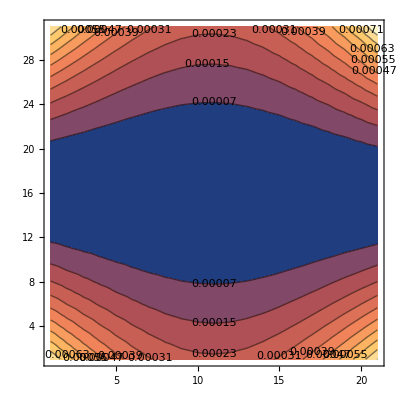

-Graphics3D-

```mathematica
ListContourPlot[disco001,PlotRange->All,Contours->10,ContourLabels->True]
ListPlot3D[disco001,PlotRange->All]
```

```mathematica
Dimensions[entro001]
```

{31,21}

## Mutual Entropy

#### mutual entropy at J_xy = 0

```mathematica
nn = 16
Entdat = {
entro10[[nn]],
entro50[[nn]],
entro375[[nn]],
entro25[[nn]],
entro1725[[nn]],
entro125[[nn]],
entro1[[nn]],
entro075[[nn]],
entro05[[nn]],
entro025[[nn]],
entro01[[nn]],
entro0075[[nn]],
entro005[[nn]],
entro0025[[nn]],
entro00125[[nn]],
entro001[[nn]]}//Transpose;

Discodat = {disco10[[nn]],
disco50[[nn]],
disco375[[nn]],
disco25[[nn]],
disco1725[[nn]],
disco125[[nn]],
disco1[[nn]],
disco075[[nn]],
disco05[[nn]],
disco025[[nn]],
disco01[[nn]],
disco0075[[nn]],
disco005[[nn]],
disco0025[[nn]],
disco00125[[nn]],
disco001[[nn]]}//Transpose;

DiscoEdat = {discoE10[[nn]],
discoE50[[nn]],
discoE375[[nn]],
discoE25[[nn]],
discoE1725[[nn]],
discoE125[[nn]],
discoE1[[nn]],
discoE075[[nn]],
discoE05[[nn]],
discoE025[[nn]],
discoE01[[nn]],
discoE0075[[nn]],
discoE005[[nn]],
discoE0025[[nn]],
discoE00125[[nn]],
discoE001[[nn]]}//Transpose;


palate = 91;
ColorData[palate,"ColorList"]
c1 = ColorData[palate,"ColorList"][[8]]
c2 = ColorData[palate,"ColorList"][[10]]
c3 = ColorData[palate,"ColorList"][[3]];
p1 = ListLogLinearPlot[
{{gamval,Entdat[[1]]}//Transpose,
{gamval,Entdat[[-1]]}//Transpose,
{gamval,Entdat[[11]]}//Transpose,
{gamval,Discodat[[1]]}//Transpose,
{gamval,Discodat[[-1]]}//Transpose,
{gamval,Discodat[[11]]}//Transpose,
{gamval,DiscoEdat[[1]]}//Transpose,
{gamval,DiscoEdat[[-1]]}//Transpose,
{gamval,DiscoEdat[[11]]}//Transpose
},Joined->True,
AxesLabel->{"γ","I(A|B)"},
Ticks->{{0.001,0.01,0.1,1},Automatic},
TicksStyle->Directive[12],
LabelStyle->16,
PlotMarkers->None,
AspectRatio->1,
PlotLabel->"J_xy=0",
(*PlotLabels->Placed[{"ξ = -1","ξ = 1","ξ = 0"},Above],*)
PlotStyle->{c1,c2,c3,{Dashed,c1},{Dashed,c2},{Dashed,c3},{Dotted,c1},{Dotted,c2},{Dotted,c3}}]

Im1 = Interpolation[{gamval,Entdat[[1]]}//Transpose,InterpolationOrder->1];
Dm1 = Interpolation[{gamval,Discodat[[1]]}//Transpose,InterpolationOrder->1];

I0 = Interpolation[{gamval,Entdat[[11]]}//Transpose,InterpolationOrder->1];
D0 = Interpolation[{gamval,Discodat[[11]]}//Transpose,InterpolationOrder->1];

I1 = Interpolation[{gamval,Entdat[[-1]]}//Transpose,InterpolationOrder->1];
D1 = Interpolation[{gamval,Discodat[[-1]]}//Transpose,InterpolationOrder->1];


p2 = LogLinearPlot[{Im1[x],Dm1[x],I1[x],D1[x],I0[x],D0[x]},{x,0.001,1},Filling->{2->{1},4->{3},6-> {5}},PlotStyle->{None,{Dashed,c1},None,{Dashed,c2},None,{Dashed,c3},{Dotted,c1},{Dotted,c2},{Dotted,c3}}];

Show[{p1,p2}]

Export[figdir<>"/Mutual_entro_at_Jxy=0_vs_escapement_rate-hold.pdf",%]




ListLogLinearPlot[{
{gamval,Discodat[[1]]/Entdat[[1]]}//Transpose,
{gamval,Discodat[[-1]]/Entdat[[-1]]}//Transpose
},Joined-> True,
PlotMarkers->Automatic,
AxesLabel->{"γ","f_Q"},
AspectRatio->1,
PlotStyle->{c1,c2,c3,{Dashed,c1},{Dashed,c2},{Dashed,c3}},
LabelStyle->18]

Export[figdir<>"/Entropy_fraction_at_Jxy=0_vs_escapement_rate.pdf",%]
```

16

{Hue[0.58, 0.67, 0.66],Hue[0.17, 1, 0.66],Hue[0.45, 0.75, 0.6],Hue[0.12, 0.7, 0.7],Hue[0.25, 0.7, 0.6],Hue[0.58, 0.5, 0.8],Hue[0.11, 1, 0.66],Hue[0.06, 0.75, 0.88],Hue[0.5, 0.5, 0.44],Hue[0.67, 0.33, 0.66]}

Hue[0.06, 0.75, 0.88]

Hue[0.67, 0.33, 0.66]

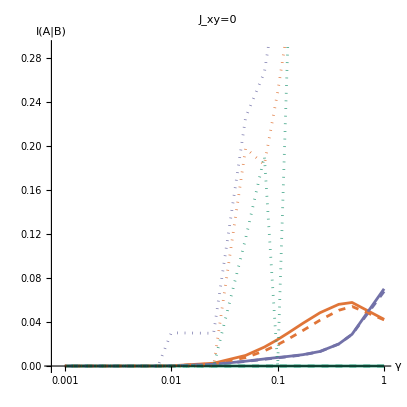

-Graphics-

#### mutual entropy at J_xy = -1

1

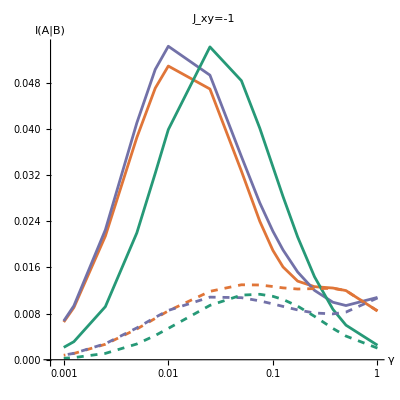

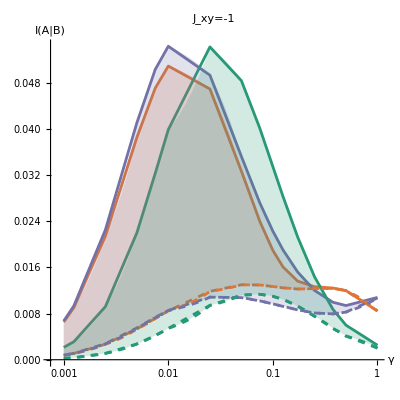

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_entro_at_Jxy=-1_vs_escapement_rate.pdf

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Entropy_fraction_at_Jxy=-1_vs_escapement_rate.pdf

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_entro_at_Jxy=-1_vs_escapement_rate.pdf

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Entropy_fraction_at_Jxy=-1_vs_escapement_rate.pdf

```mathematica
nn = 1
Entdat = {
entro10[[nn]],
entro50[[nn]],
entro375[[nn]],
entro25[[nn]],
entro1725[[nn]],
entro125[[nn]],
entro1[[nn]],
entro075[[nn]],
entro05[[nn]],
entro025[[nn]],
entro01[[nn]],
entro0075[[nn]],
entro005[[nn]],
entro0025[[nn]],
entro00125[[nn]],
entro001[[nn]]}//Transpose;

Discodat = {disco10[[nn]],
disco50[[nn]],
disco375[[nn]],
disco25[[nn]],
disco1725[[nn]],
disco125[[nn]],
disco1[[nn]],
disco075[[nn]],
disco05[[nn]],
disco025[[nn]],
disco01[[nn]],
disco0075[[nn]],
disco005[[nn]],
disco0025[[nn]],
disco00125[[nn]],
disco001[[nn]]}//Transpose;



ColorData[palate,"ColorList"];
c1 = ColorData[palate,"ColorList"][[8]];
c2 = ColorData[palate,"ColorList"][[10]];
c3 = ColorData[palate,"ColorList"][[3]];
p1 = ListLogLinearPlot[
{{gamval,Entdat[[1]]}//Transpose,
{gamval,Entdat[[-1]]}//Transpose,
{gamval,Entdat[[11]]}//Transpose,
{gamval,Discodat[[1]]}//Transpose,
{gamval,Discodat[[-1]]}//Transpose,
{gamval,Discodat[[11]]}//Transpose
},Joined->True,
AxesLabel->{"γ","I(A|B)"},
Ticks->{{0.001,0.01,0.1,1},Automatic},
TicksStyle->Directive[12],
LabelStyle->16,
PlotMarkers->None,
AspectRatio->1,
PlotLabel->"J_xy=-1",
(*PlotLabels->Placed[{"ξ = -1","ξ = 1","ξ = 0"},Above],*)
PlotStyle->{c1,c2,c3,{Dashed,c1},{Dashed,c2},{Dashed,c3}}]

Im1 = Interpolation[{gamval,Entdat[[1]]}//Transpose,InterpolationOrder->1];
Dm1 = Interpolation[{gamval,Discodat[[1]]}//Transpose,InterpolationOrder->1];

I0 = Interpolation[{gamval,Entdat[[11]]}//Transpose,InterpolationOrder->1];
D0 = Interpolation[{gamval,Discodat[[11]]}//Transpose,InterpolationOrder->1];

I1 = Interpolation[{gamval,Entdat[[-1]]}//Transpose,InterpolationOrder->1];
D1 = Interpolation[{gamval,Discodat[[-1]]}//Transpose,InterpolationOrder->1];


p2 = LogLinearPlot[{Im1[x],Dm1[x],I1[x],D1[x],I0[x],D0[x]},{x,0.001,1},Filling->{2->{1},4->{3},6-> {5}},PlotStyle->{None,{Dashed,c1},None,{Dashed,c2},None,{Dashed,c3}}];

Show[{p1,p2}]

Export[figdir<>"/Mutual_entro_at_Jxy=-1_vs_escapement_rate.pdf",%]




Export[figdir<>"/Entropy_fraction_at_Jxy=-1_vs_escapement_rate.pdf",%]
```

#### mutual entropy at J_xy = +1

-1

Hue[0.06, 0.75, 0.88]

Hue[0.67, 0.33, 0.66]

Hue[0.45, 0.75, 0.6]

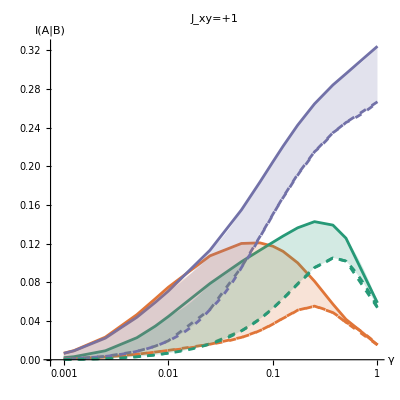

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_entro_at_Jxy=+1_vs_escapement_rate.pdf

-Graphics-

```mathematica
nn = -1
Entdat = {
entro10[[nn]],
entro50[[nn]],
entro375[[nn]],
entro25[[nn]],
entro1725[[nn]],
entro125[[nn]],
entro1[[nn]],
entro075[[nn]],
entro05[[nn]],
entro025[[nn]],
entro01[[nn]],
entro0075[[nn]],
entro005[[nn]],
entro0025[[nn]],
entro00125[[nn]],
entro001[[nn]]}//Transpose;

Discodat = {disco10[[nn]],
disco50[[nn]],
disco375[[nn]],
disco25[[nn]],
disco1725[[nn]],
disco125[[nn]],
disco1[[nn]],
disco075[[nn]],
disco05[[nn]],
disco025[[nn]],
disco01[[nn]],
disco0075[[nn]],
disco005[[nn]],
disco0025[[nn]],
disco00125[[nn]],
disco001[[nn]]}//Transpose;



ColorData[palate,"ColorList"];
c1 = ColorData[palate,"ColorList"][[8]]
c2 = ColorData[palate,"ColorList"][[10]]
c3 = ColorData[palate,"ColorList"][[3]]
p1 = ListLogLinearPlot[
{{gamval,Entdat[[1]]}//Transpose,
{gamval,Entdat[[-1]]}//Transpose,
{gamval,Entdat[[11]]}//Transpose,
{gamval,Discodat[[1]]}//Transpose,
{gamval,Discodat[[-1]]}//Transpose,
{gamval,Discodat[[11]]}//Transpose
},
Joined->True,
(* Filling->Axis,*)
Ticks->{{0.001,0.01,0.1,1},Automatic},
TicksStyle->Directive[12],
LabelStyle->16,
AxesLabel->{"γ","I(A|B)"},
PlotMarkers->None,
AspectRatio->1,
PlotLabel->"J_xy=+1",
(*PlotLabels->Placed[{"ξ = -1","ξ = 1","ξ = 0"},Above],*)
PlotStyle->{c1,c2,c3,{Dashed,c1},{Dashed,c2},{Dashed,c3}},
Filling->{1->{4},2->{5},3->{6}}];

Im1 = Interpolation[{gamval,Entdat[[1]]}//Transpose,InterpolationOrder->1];
Dm1 = Interpolation[{gamval,Discodat[[1]]}//Transpose,InterpolationOrder->1];

I0 = Interpolation[{gamval,Entdat[[11]]}//Transpose,InterpolationOrder->1];
D0 = Interpolation[{gamval,Discodat[[11]]}//Transpose,InterpolationOrder->1];

I1 = Interpolation[{gamval,Entdat[[-1]]}//Transpose,InterpolationOrder->1];
D1 = Interpolation[{gamval,Discodat[[-1]]}//Transpose,InterpolationOrder->1];


p2 = LogLinearPlot[{Im1[x],Dm1[x],I1[x],D1[x],I0[x],D0[x]},{x,0.001,1},Filling->{2->{1},4->{3},6-> {5}},PlotStyle->{None,{Dashed,c1},None,{Dashed,c2},None,{Dashed,c3}}];

Show[{p1,p2}]


Export[figdir<>"/Mutual_entro_at_Jxy=+1_vs_escapement_rate.pdf",%]
```

-1

{Hue[0.58, 0.67, 0.66],Hue[0.17, 1, 0.66],Hue[0.45, 0.75, 0.6],Hue[0.12, 0.7, 0.7],Hue[0.25, 0.7, 0.6],Hue[0.58, 0.5, 0.8],Hue[0.11, 1, 0.66],Hue[0.06, 0.75, 0.88],Hue[0.5, 0.5, 0.44],Hue[0.67, 0.33, 0.66]}

Hue[0.06, 0.75, 0.88]

Hue[0.67, 0.33, 0.66]

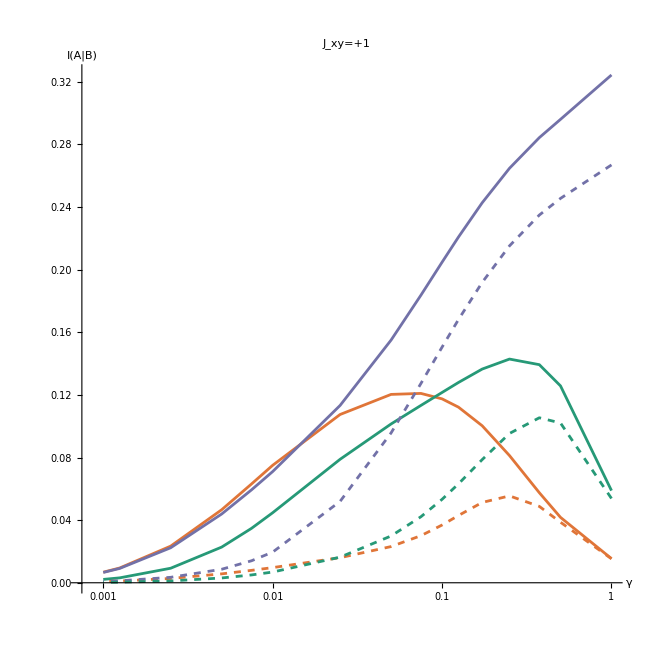

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Mutual_entro_at_Jxy=+1_vs_escapement_rate.pdf

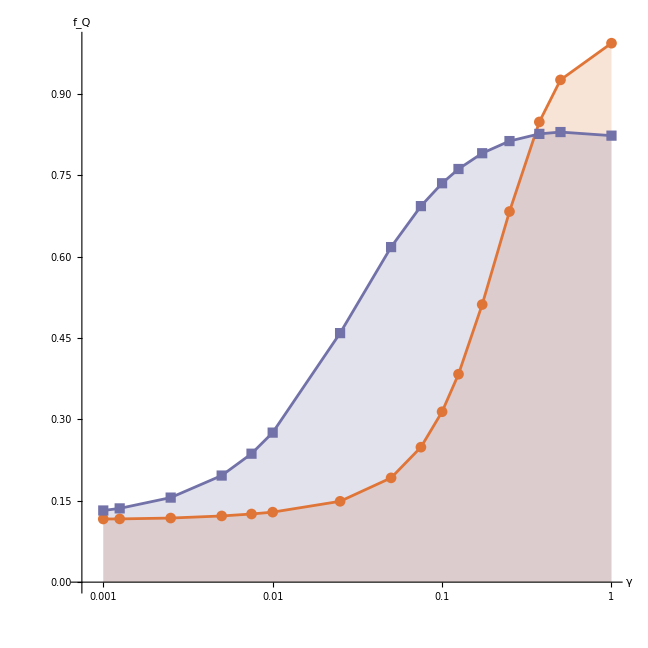

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Entropy_fraction_at_Jxy=-1_vs_escapement_rate.pdf

```mathematica
ListLogLinearPlot[{
{gamval,Discodat[[1]]/Entdat[[1]]}//Transpose,
{gamval,Discodat[[-1]]/Entdat[[-1]]}//Transpose
},Joined-> True,
PlotMarkers->Automatic,
AxesLabel->{"γ","f_Q"},
AspectRatio->1,
PlotStyle->{c1,c2,c3,{Dashed,c1},{Dashed,c2},{Dashed,c3}},
LabelStyle->18,
Filling->Axis]

Export[figdir<>"/Entropy_fraction_at_Jxy=-1_vs_escapement_rate.pdf",%]
```

## Concurance and mutual entropy starting from bell states

{NoiseSynchro_Entropy_phi-_0.csv,NoiseSynchro_Entropy_phi-_-1.csv,NoiseSynchro_Entropy_phi-_1.csv,NoiseSynchro_Entropy_psi-_0.csv,NoiseSynchro_Entropy_psi-_-1.csv,NoiseSynchro_Entropy_psi-_1.csv}

{NoiseSynchro_Entropy_phi+_0.csv,NoiseSynchro_Entropy_phi+_-1.csv,NoiseSynchro_Entropy_phi+_1.csv,NoiseSynchro_Entropy_psi+_0.csv,NoiseSynchro_Entropy_psi+_-1.csv,NoiseSynchro_Entropy_psi+_1.csv}

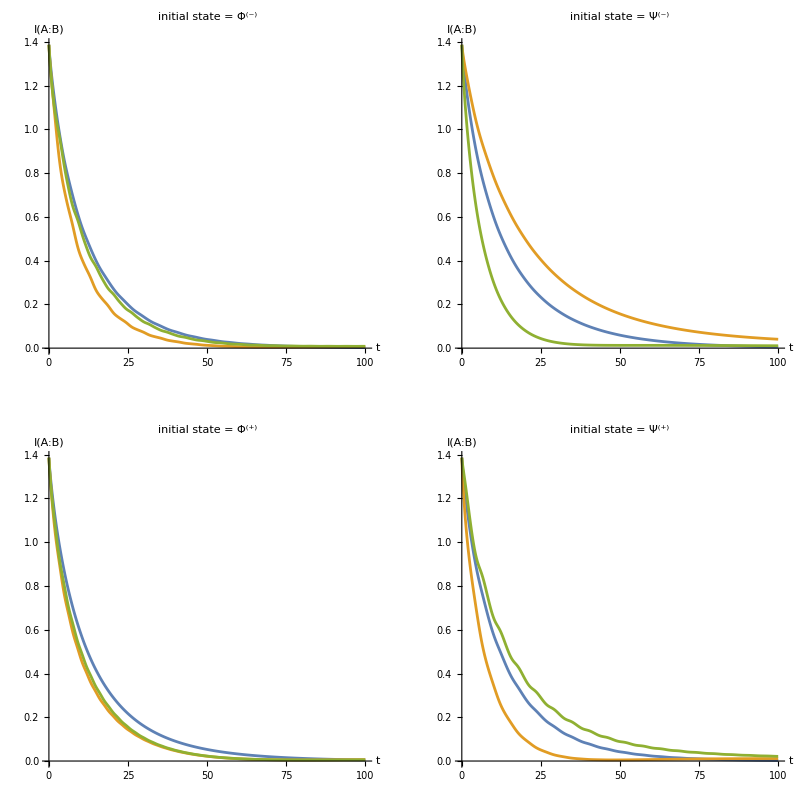

```mathematica
fn = FileNames["NoiseSynchro_Entropy_p*-_*.csv"]
dd = Table[Import[fn[[i]]],{i,6}];


legends = {"ξ=0","ξ=-1","ξ=+1"};
legends = None;
p1 = ListPlot[{
dd[[1,1]],
dd[[2,1]],
dd[[3,1]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
AspectRatio->1,
AxesLabel->{"t","I(A:B)"},
PlotLabel->"initial state = Φ^(-)",
PlotLegends->legends];

p2 =ListPlot[{
dd[[4,1]],
dd[[5,1]],
dd[[6,1]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,AxesLabel->{"t","I(A:B)"},
PlotLegends->legends,
PlotLabel->"initial state = Ψ^(-)",
AspectRatio->1];


fn = FileNames["NoiseSynchro_Entropy_p*+_*.csv"]
dd = Table[Import[fn[[i]]],{i,6}];

p3 = ListPlot[{
dd[[1,1]],
dd[[2,1]],
dd[[3,1]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
AspectRatio->1,AxesLabel->{"t","I(A:B)"},
PlotLabel->"initial state = Φ^(+)",
PlotLegends->legends];

p4 = ListPlot[{
dd[[4,1]],
dd[[5,1]],
dd[[6,1]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
PlotLegends->legends,AxesLabel->{"t","I(A:B)"},
PlotLabel->"initial state = Ψ^(+)",
AspectRatio->1];


GraphicsGrid[{{p1,p2},{p3,p4}}]
```

{NoiseSynchro_Entropy_standard_phi-_0.csv,NoiseSynchro_Entropy_standard_phi-_-1.csv,NoiseSynchro_Entropy_standard_phi-_1.csv,NoiseSynchro_Entropy_standard_psi-_0.csv,NoiseSynchro_Entropy_standard_psi-_-1.csv,NoiseSynchro_Entropy_standard_psi-_1.csv}

{NoiseSynchro_Entropy_standard_phi+_0.csv,NoiseSynchro_Entropy_standard_phi+_-1.csv,NoiseSynchro_Entropy_standard_phi+_1.csv,NoiseSynchro_Entropy_standard_psi+_0.csv,NoiseSynchro_Entropy_standard_psi+_-1.csv,NoiseSynchro_Entropy_standard_psi+_1.csv}

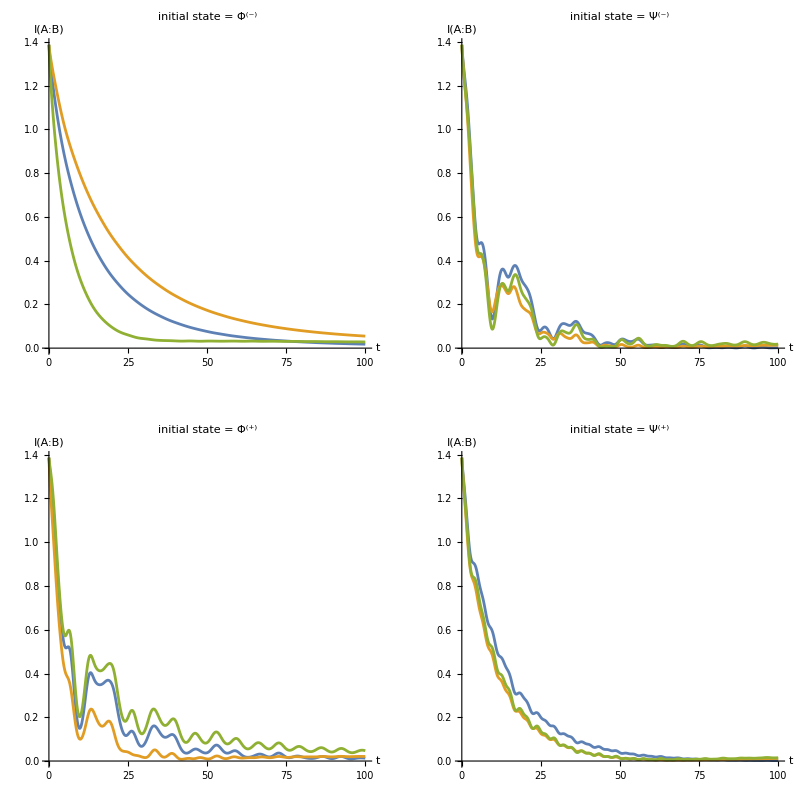

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/MutualInformation.pdf

```mathematica
fn = FileNames["NoiseSynchro_Entropy_standard_p*-_*.csv"]
dd = Table[Import[fn[[i]]],{i,6}];


legends = {"ξ=0","ξ=-1","ξ=+1"};
legends = None;
p1 = ListPlot[{
dd[[1,1]],
dd[[2,1]],
dd[[3,1]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
AspectRatio->1,
AxesLabel->{"t","I(A:B)"},
PlotLabel->"initial state = Φ^(-)",
PlotLegends->legends];

p2 =ListPlot[{
dd[[4,1]],
dd[[5,1]],
dd[[6,1]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,AxesLabel->{"t","I(A:B)"},
PlotLegends->legends,
PlotLabel->"initial state = Ψ^(-)",
AspectRatio->1];


fn = FileNames["NoiseSynchro_Entropy_standard_p*+_*.csv"]
dd = Table[Import[fn[[i]]],{i,6}];

p3 = ListPlot[{
dd[[1,1]],
dd[[2,1]],
dd[[3,1]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
AspectRatio->1,AxesLabel->{"t","I(A:B)"},
PlotLabel->"initial state = Φ^(+)",
PlotLegends->legends];

p4 = ListPlot[{
dd[[4,1]],
dd[[5,1]],
dd[[6,1]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
PlotLegends->legends,AxesLabel->{"t","I(A:B)"},
PlotLabel->"initial state = Ψ^(+)",
AspectRatio->1];


GraphicsGrid[{{p1,p2},{p3,p4}}]
Export[figdir<>"/MutualInformation.pdf",%]
```

### Degree of quantum-ness

```mathematica
Length[dd]
```

{NoiseSynchro_Entropy_standard_phi-_0.csv,NoiseSynchro_Entropy_standard_phi-_-1.csv,NoiseSynchro_Entropy_standard_phi-_1.csv,NoiseSynchro_Entropy_standard_psi-_0.csv,NoiseSynchro_Entropy_standard_psi-_-1.csv,NoiseSynchro_Entropy_standard_psi-_1.csv}

6

{NoiseSynchro_Entropy_standard_phi-_0.csv,NoiseSynchro_Entropy_standard_phi-_-1.csv,NoiseSynchro_Entropy_standard_phi-_1.csv,NoiseSynchro_Entropy_standard_psi-_0.csv,NoiseSynchro_Entropy_standard_psi-_-1.csv,NoiseSynchro_Entropy_standard_psi-_1.csv}

{NoiseSynchro_Entropy_standard_phi+_0.csv,NoiseSynchro_Entropy_standard_phi+_-1.csv,NoiseSynchro_Entropy_standard_phi+_1.csv,NoiseSynchro_Entropy_standard_psi+_0.csv,NoiseSynchro_Entropy_standard_psi+_-1.csv,NoiseSynchro_Entropy_standard_psi+_1.csv}

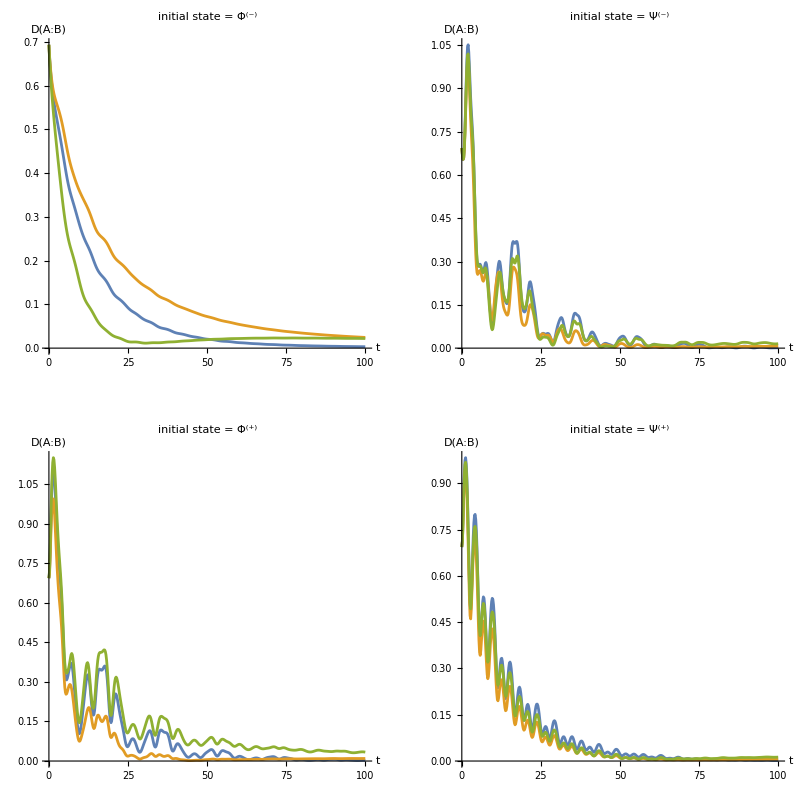

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/Degree_of_quantumness.pdf

```mathematica
fn = FileNames["NoiseSynchro_Entropy_standard_p*-_*.csv"]
dd = Table[Import[fn[[i]]],{i,6}];

legends = {"ξ=0","ξ=-1","ξ=+1"};
legends = None;
p1 = ListPlot[{
dd[[1,5]],
dd[[2,5]],
dd[[3,5]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
AspectRatio->1,
AxesLabel->{"t","D(A:B)"},
PlotLabel->"initial state = Φ^(-)",
PlotLegends->legends];

p2 =ListPlot[{
dd[[4,5]],
dd[[5,5]],
dd[[6,5]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,AxesLabel->{"t","D(A:B)"},
PlotLegends->legends,
PlotLabel->"initial state = Ψ^(-)",
AspectRatio->1];


fn = FileNames["NoiseSynchro_Entropy_standard_p*+_*.csv"]
dd = Table[Import[fn[[i]]],{i,6}];

p3 = ListPlot[{
dd[[1,5]],
dd[[2,5]],
dd[[3,5]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
AspectRatio->1,AxesLabel->{"t","D(A:B)"},
PlotLabel->"initial state = Φ^(+)",
PlotLegends->legends];

p4 = ListPlot[{
dd[[4,5]],
dd[[5,5]],
dd[[6,5]]
},
PlotRange->All,Joined->True,
DataRange->{0,100},
LabelStyle->16,
PlotLegends->legends,AxesLabel->{"t","D(A:B)"},
PlotLabel->"initial state = Ψ^(+)",
AspectRatio->1];


GraphicsGrid[{{p1,p2},{p3,p4}}]
Export[figdir<>"/Degree_of_quantumness.pdf",%]
```

## Phase Synchronization plots

```mathematica
df = FileNames["Noise_Synchro*_gamma=0.01.csv"]
{sx1,sy1,sz1,sx2,sy2,sz2} = Table[Import[df[[i]]],{i,6}];
```

{Noise_Synchro1x_gamma=0.01.csv,Noise_Synchro1y_gamma=0.01.csv,Noise_Synchro1z_gamma=0.01.csv,Noise_Synchro2x_gamma=0.01.csv,Noise_Synchro2y_gamma=0.01.csv,Noise_Synchro2z_gamma=0.01.csv}

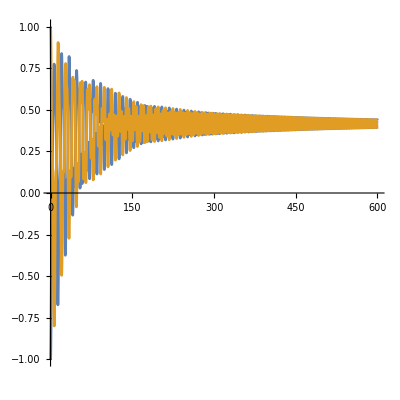

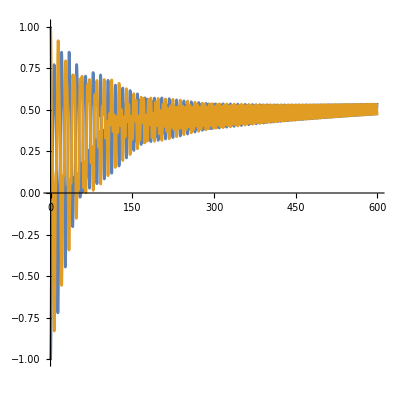

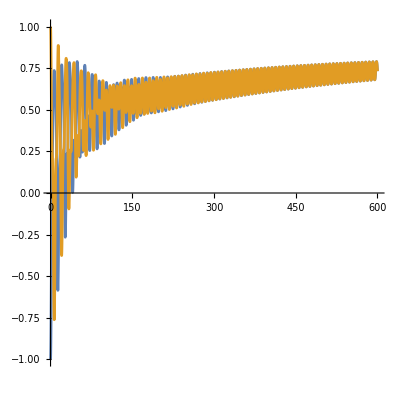

```mathematica
ListPlot[{sz1[[1]],sz2[[1]]},Joined->True,PlotRange->{-1,1},DataRange->{0,600},AspectRatio->1,LabelStyle->16]
ListPlot[{sz1[[11]],sz2[[11]]},Joined->True,PlotRange->{-1,1},DataRange->{0,600},AspectRatio->1,LabelStyle->16]
ListPlot[{sz1[[-1]],sz2[[-1]]},Joined->True,PlotRange->{-1,1},DataRange->{0,600},AspectRatio->1,LabelStyle->16]
```

```mathematica
Hilbert
```

```mathematica
Length[sx1]
```

101

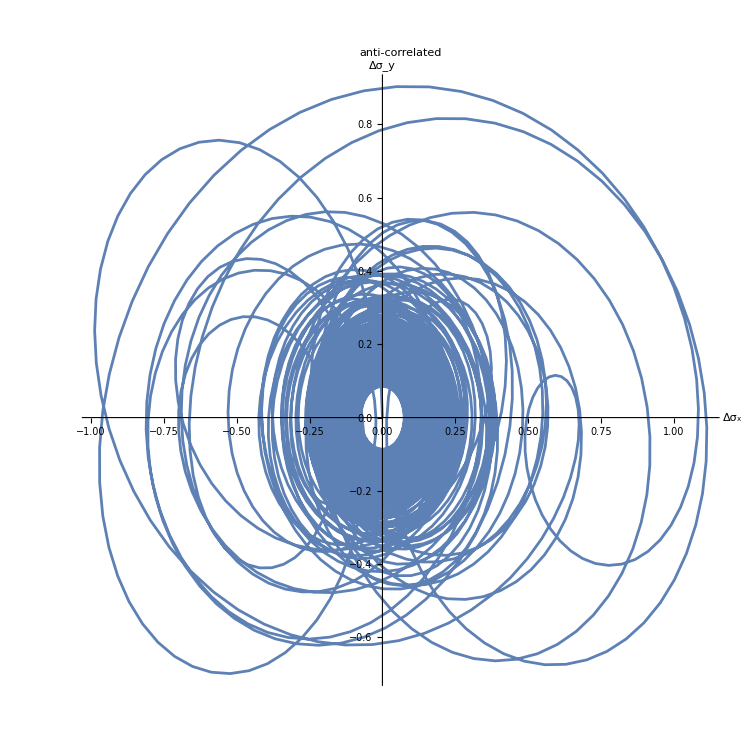

```mathematica
p1= ListPlot[{Transpose[{sx1[[1]]-sx2[[1]],sy1[[1]]-sy2[[1]]}]},
Joined->True,PlotRange->All,AspectRatio->1,LabelStyle->20,
PlotLabel->"anti-correlated",
AxesLabel->{"Δσ_x","Δσ_y"}]
```

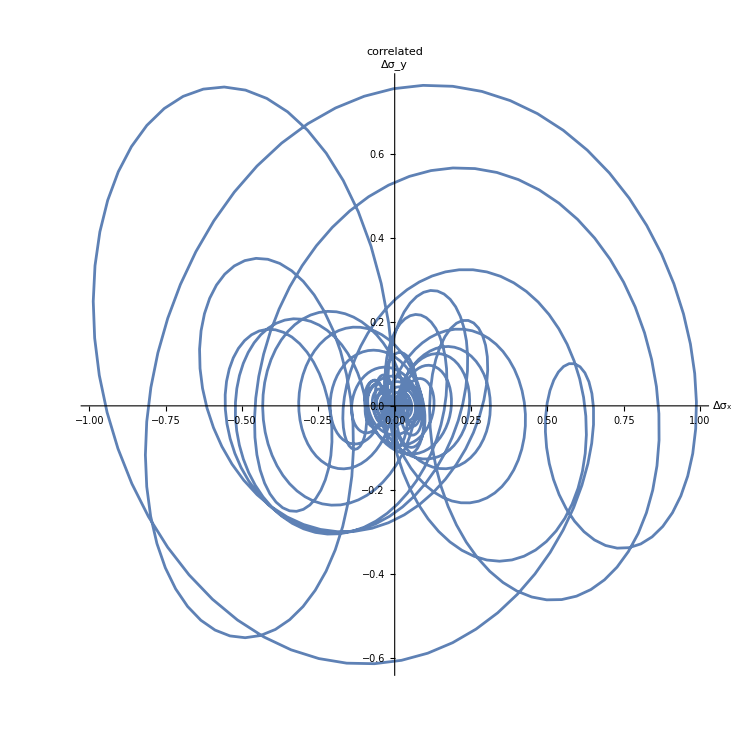

```mathematica
p2 = ListPlot[{Transpose[{sx1[[-1]]-sx2[[-1]],sy1[[-1]]-sy2[[-1]]}]},
Joined->True,PlotRange->All,AspectRatio->1,LabelStyle->20,
PlotLabel->"correlated",
AxesLabel->{"Δσ_x","Δσ_y"}]
```

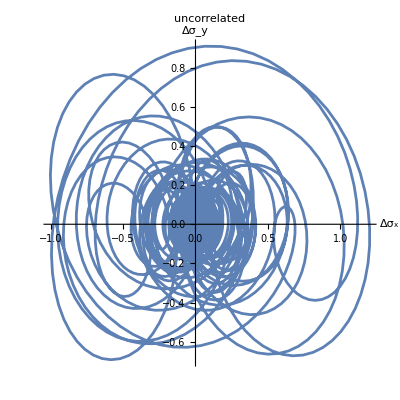

```mathematica
p3 = ListPlot[{Transpose[{sx1[[51]]-sx2[[51]],sy1[[51]]-sy2[[51]]}]},Joined->True,PlotRange->All,AspectRatio->1,LabelStyle->20,
PlotLabel->"uncorrelated",
AxesLabel->{"Δσ_x","Δσ_y"}]
```

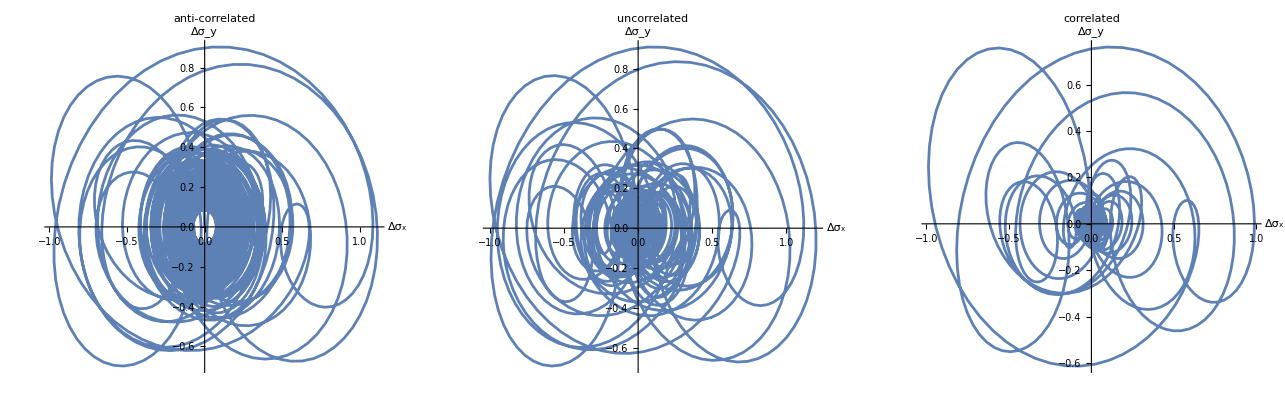

/Users/bittner/Library/CloudStorage/Dropbox/Apps/Overleaf/Spontaneous Synchronization of Quantum Clocks/Figures/XY-projection.pdf

```mathematica
GraphicsGrid[{{p1,p3,p2}},ImageSize->Large]
Export[figdir<>"/XY-projection.pdf",%]
```

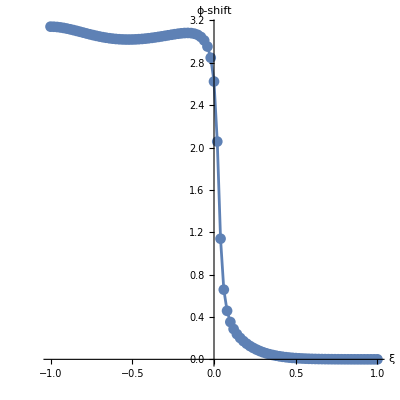

```mathematica
op = Import["Noise_Synchro_order_param_gamma=0.005.csv"];
ListPlot[Flatten[op],Joined->True,PlotMarkers->Automatic,DataRange->{-1,1},PlotRange->{0,π},AspectRatio->1,LabelStyle->20,
AxesLabel->{"ξ","ϕ-shift"}]
```

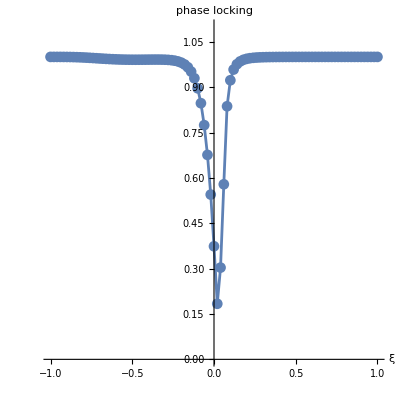

```mathematica
plv = Import["Noise_Synchro_PLV_gamma=0.005.csv"];
ListPlot[Flatten[plv],Joined->True,PlotMarkers->Automatic,DataRange->{-1,1},PlotRange->{0,1.1},AspectRatio->1,LabelStyle->20,
AxesLabel->{"ξ","phase locking"}]
```

```mathematica
Log[10,2^200]//N
```

60.206